### Recordatorio: ¿para qué sirve la función de reshuffle? Hablemos de la física...

El reshuffle es un transformación para calcular la matriz de Choi de un canal cuántico ℰ a partir de la forma de superoperador de ℰ (la forma matricial).

### Matriz de Choi y completa positividad de ℰ

La matriz de Choi también se define como el canal ℰ aplicado al estado máximamente entrelazado del sistema extendido, ℰ(ρ^ϕ)= matriz de Choi de ℰ.

La matriz de Choi es importante porque si ℰ(ρ^ϕ) es positiva semidefinida, entonces ℰ es completamente positivo. La completa positividad es la condición extra que ℰ debe de cumplir para ser un canal cuántico. 

Ejemplo: 
Supongamos que ℰ es una operación lineal de 1 qubit. Para saber si ℰ es completamente positiva se debe evaluar si ℰ[1/2(00+11)(00+11)] es una matriz positiva.

### Para qubits, la matriz de Choi es dimensión 2^(2n), donde n es el número de qubits en el sistema.

### Matriz de Choi como transformación que reordena

```mathematica
(mat=Table[ConstantArray[i,4],{i,1,4}])//MatrixForm
```

(1 | 1 | 1 | 1
2 | 2 | 2 | 2
3 | 3 | 3 | 3
4 | 4 | 4 | 4)

```mathematica
Reshuffle[mat]//MatrixForm
```

```mathematica
(mat=Table[ConstantArray[i,16],{i,1,16}])//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11
12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12
13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13
14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14
15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15
16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16)

```mathematica
Reshuffle[mat]//MatrixForm
```

### Versiones de la función Reshuffle

#### Versión 1 (JA)

```mathematica
ReshuffleV1[A_]:=ArrayFlatten[ArrayFlatten/@Partition[Partition[ArrayReshape[#,{Sqrt[Dimensions[A][[1]]],Sqrt[Dimensions[A][[1]]]}]&/@A,Sqrt[Dimensions[A][[1]]]],Sqrt[Dimensions[A][[1]]]],1]
```

#### Versión 2 (JA)

```mathematica
ReshuffleV2[A_]:=
Module[{fourIndNot,newIndices,dim},
dim=Length[A];
fourIndNot=Outer[{#1,#2}&,Tuples[Range[√dim],2],Tuples[Range[√dim],2],1];
newIndices=Table[FlattenAt[Position[fourIndNot,Transpose[fourIndNot,3<->4][[i,j]]],1],{i,dim},{j,dim}];
Table[A[[newIndices[[i,j,1]],newIndices[[i,j,2]]]],{i,dim},{j,dim}]
]
```

#### Versión 3 (Subadra)

```mathematica
ReshuffleV3[A_]:=Module[{F1},
F1=ArrayReshape[A,{#,#,#,#}]&[Sqrt[Length[A]]];
ArrayFlatten[F1]
]
```

#### Versión 4 (JA)

```mathematica
ReshuffleV4[E_List]:=Module[{dimSubMatrix,subMatrices},
dimSubMatrix=√Length[E];
subMatrices=ArrayReshape[#,{dimSubMatrix,dimSubMatrix}]&/@E;
ArrayFlatten[Partition[subMatrices,dimSubMatrix]]
]
```

### Rendimiento

#### Memoria

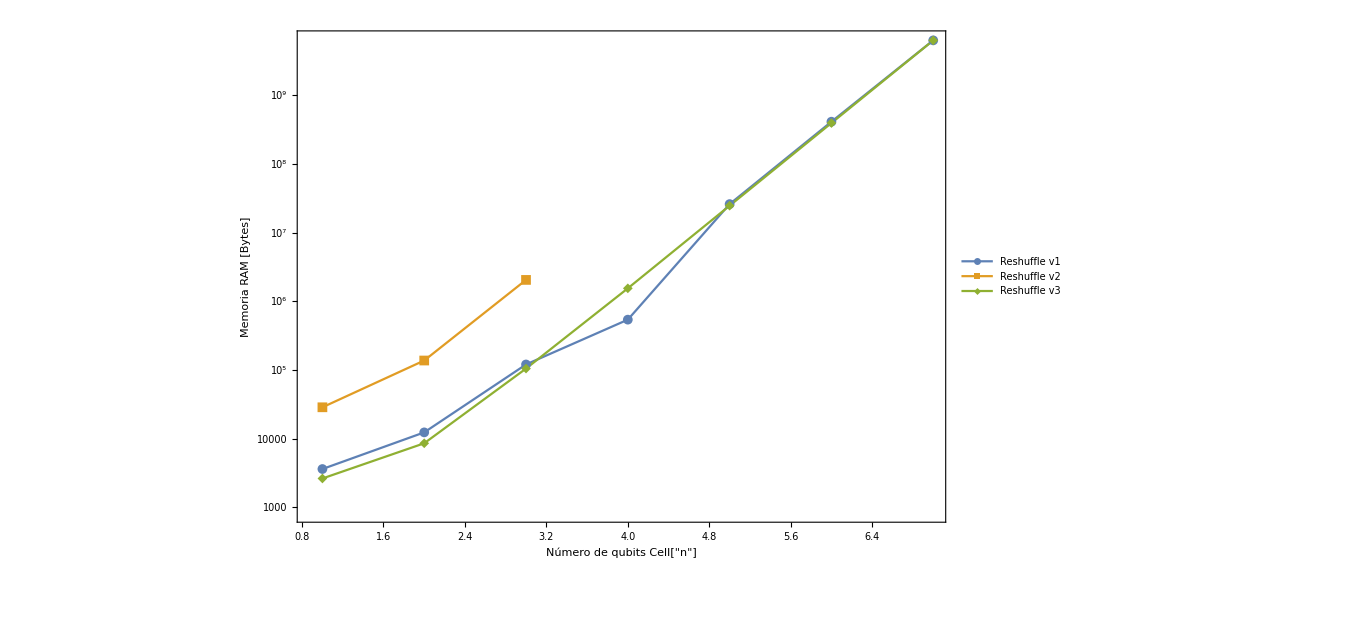

```mathematica
memory=ListLogPlot[{reshuffle[[;;,2]],reshuffleV2[[;;,2]],reshuffleSub[[;;,2]]},Joined->True,PlotMarkers->{Automatic, Medium},PlotRange->All,PlotLegends->{Style["Reshuffle v1","Text"],Style["Reshuffle v2","Text"],Style["Reshuffle v3","Text"]},PlotStyle->PointSize[Medium],ImageSize->1000,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{Style["Memoria RAM [Bytes]",Bold,Black,22],None},{Style["Número de qubits Cell["n",ExpressionUUID->"fb0fcc9f-a565-4eab-8a97-6d70f04f55e4"]",Bold,Black,22],None}},FrameTicks->All]
```

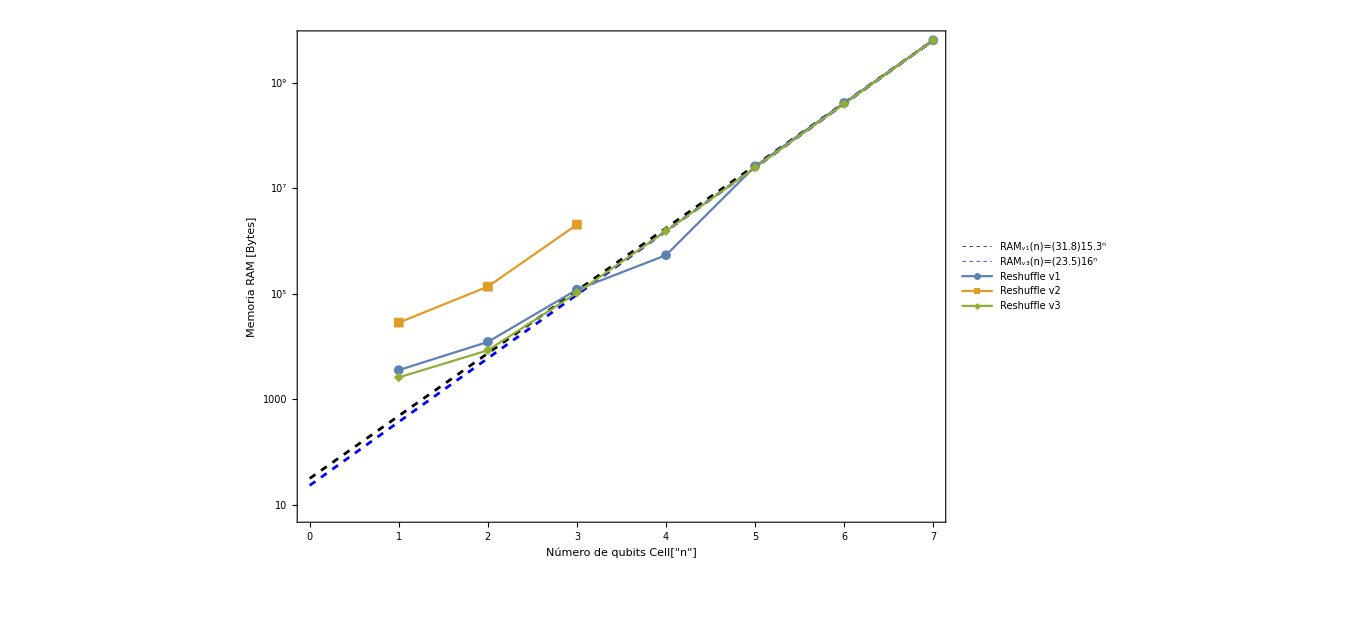

```mathematica
Show[mem2,mem,memory]
```

#### Tiempo de ejecución

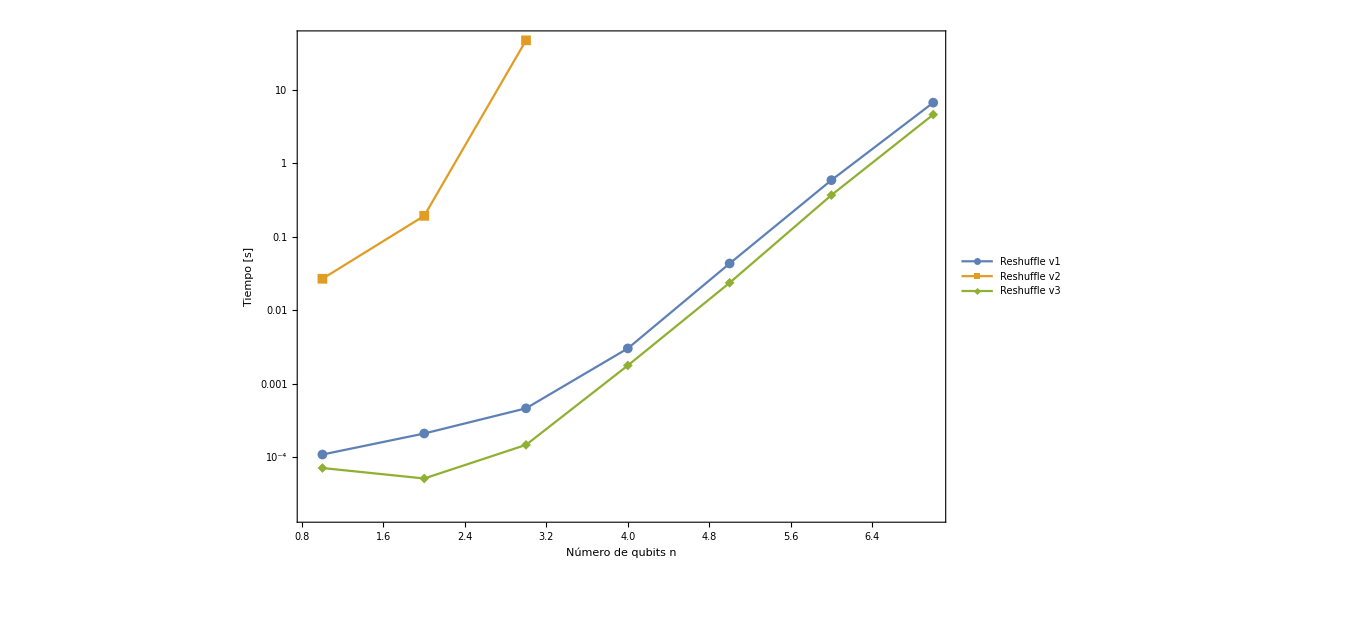

```mathematica
tiempos=ListLogPlot[{v1,v2,v3},PlotStyle->PointSize[Medium],PlotRange->All,PlotLegends->{Style["Reshuffle v1","Text"],Style["Reshuffle v2","Text"],Style["Reshuffle v3","Text"]},ImageSize->1000,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{Style["Tiempo [s]",Bold,Black,25],None},{Style["Número de qubits n",Bold,Black,25],None}},FrameTicks->All,Joined->True,PlotMarkers->{Automatic,Medium}]
```

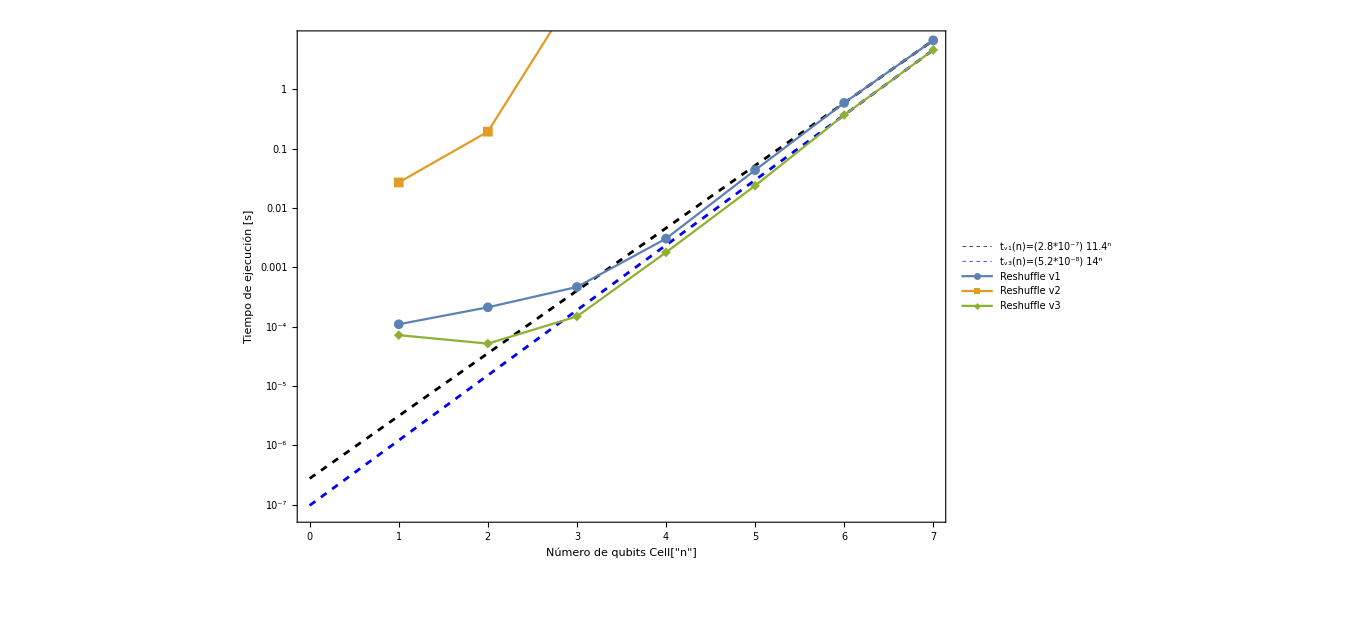

```mathematica
Show[t,t3,tiempos]
```

### Conclusiones

1. Las versiones 1 y 3 tienen rendimientos similares, especialmente cuando el número de qubits se hace cada vez más grande. 
2. La versión 3 es un código más limpio y que aprovecha mejor las funciones del lenguaje de Wolfram.
3. La versión 3 es la mejor y ganadora.

## Pendejeando:

```mathematica
Table[AbsoluteTiming[MaxMemoryUsed[ReshuffleV3[Table[ConstantArray[i,4^n],{i,1,4^n}]]]],{n,1,7}]
```

{{0.000168,4104},{0.000232,16376},{0.001251,170448},{0.006281,1540336},{0.021045,24644064},{0.234548,394266936},{3.20956,6308235544}}

```mathematica
Table[AbsoluteTiming[MaxMemoryUsed[ReshuffleV4[Table[ConstantArray[i,4^n],{i,1,4^n}]]]],{n,1,7}]
```

{{0.000081,4400},{0.000076,12584},{0.000218,116856},{0.001179,1677760},{0.005892,25998064},{0.189166,412325768},{1.53239,6315971656}}